```mathematica
Integrate[1/7*(1-Exp[-3(7-x)]),{x,0,7}]
```

1/21 (20+1/ⅇ^21)

```mathematica
Integrate[1/F*(1-Exp[-l*(Floor[(k+x)/F]*F-x)]),{x,0,F}]
```

∫_0^F (1-ⅇ^(-l (-x+F Floor[(k+x)/F])))/F ⅆx

```mathematica
(-1+ⅇ^(-k T)+k T)/(k T)
```

(-1+ⅇ^(-k T)+k T)/(k T)

```mathematica
ds = Import["C:\\Users\\Rohan Bapat\\Documents\\Projects\\Immunization Supply Chain\\immunization_supply_chain\\inputs\\total_delay_cdf.csv","Dataset"]
```

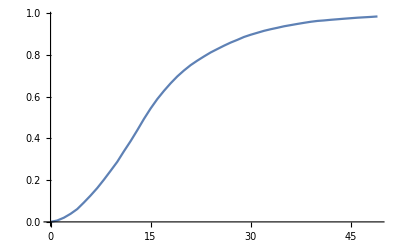

```mathematica
ListLinePlot[ds]
```

```mathematica
f=15
l=0.1
```

15

0.1

```mathematica
Clear[k]
```

```mathematica
g[x_]:=Piecewise[{{1-Exp[-l*x] ,x>=0},{0,x<0}}]
```

```mathematica
pk = Integrate[1/f*g[Floor[(k+x)/f]*f-x],{x,0,f}]
```

∫_0^15 1/15 (Piecewise[{{1-ⅇ^(-0.1 (-x+15 Floor[(k+x)/15])), -x+15 Floor[(k+x)/15]≥0}, {0, True}}])ⅆx

```mathematica
Simplify[pk]
```

∫_0^15 1/15 (Piecewise[{{1-ⅇ^(0.1 x-1.5 Floor[0.0666667 (k+x)]), x≤15 Floor[(k+x)/15]}, {0, True}}])ⅆx

```mathematica
k=30
```

30

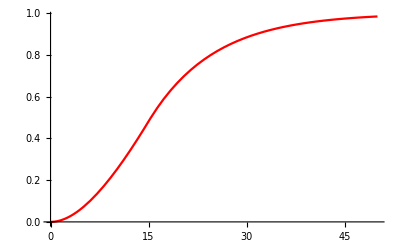

```mathematica
Plot[pk,{k,0,50}, PlotStyle->Red]
```

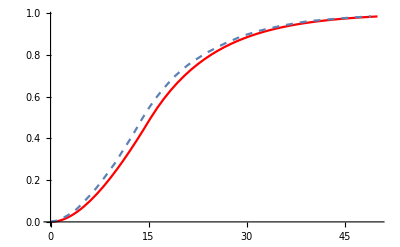

```mathematica
Show[Plot[pk,{k,0,50}, PlotStyle->Red],ListLinePlot[ds, PlotStyle->Dashed]]
```

```mathematica
Clear[k]
```

```mathematica
k
```

1

```mathematica
wy= 1/f*Integrate[Sum[g[k*f-x]-g[k*f-x-y],{k,1,5}],{x,0,f}]
```

1/15 (Piecewise[{{65.0055, y>75.}, {9.99447 (-1.+ⅇ^(0.1 y)), y≤0.}, {0.000553084 (10.-10. ⅇ^(0.1 y)+1808.04 y), 0.<y<15.||15.<y<30.||30.<y<45.||45.<y<60.||60.<y<75.}, {5. ⅇ^(-6.-0.1 y) (418770.-2. ⅇ^(1.5+0.1 y)-2. ⅇ^(3.+0.1 y)-2. ⅇ^(4.5+0.1 y)-62. ⅇ^(6.+0.1 y)-2. ⅇ^(0.1 y)+ⅇ^(6.+0.1 y) y), y==75.}, {2. ⅇ^(-6.-0.1 y) (11630.3-10. ⅇ^(1.5+0.1 y)-10. ⅇ^(3.+0.1 y)-10. ⅇ^(4.5+0.1 y)-20. ⅇ^(6.+0.1 y)+5. ⅇ^(1.5+0.2 y)+5. ⅇ^(3.+0.2 y)-5. ⅇ^(0.1 y)+5. ⅇ^(0.2 y)+ⅇ^(6.+0.1 y) y), y==30.}, {ⅇ^(-6.-0.1 y) (5190.13-20. ⅇ^(1.5+0.1 y)-20. ⅇ^(3.+0.1 y)-20. ⅇ^(4.5+0.1 y)-10. ⅇ^(6.+0.1 y)+10. ⅇ^(1.5+0.2 y)+10. ⅇ^(3.+0.2 y)+10. ⅇ^(4.5+0.2 y)-20. ⅇ^(0.1 y)+10. ⅇ^(0.2 y)+ⅇ^(6.+0.1 y) y), y==15.}, {2. ⅇ^(-6.-0.1 y) (233600.-5. ⅇ^(1.5+0.1 y)-5. ⅇ^(3.+0.1 y)-10. ⅇ^(4.5+0.1 y)-95. ⅇ^(6.+0.1 y)-5. ⅇ^(0.1 y)+5. ⅇ^(0.2 y)+2. ⅇ^(6.+0.1 y) y), y==60.}, {ⅇ^(-6.-0.1 y) (104247.-10. ⅇ^(1.5+0.1 y)-20. ⅇ^(3.+0.1 y)-20. ⅇ^(4.5+0.1 y)-100. ⅇ^(6.+0.1 y)+10. ⅇ^(1.5+0.2 y)-10. ⅇ^(0.1 y)+10. ⅇ^(0.2 y)+3. ⅇ^(6.+0.1 y) y), True}}])

```mathematica
y=15
```

15

```mathematica
1/f*Integrate[Sum[g[k*f-x]-g[k*f-x-y],{k,1,5}],{x,0,f}]
```

0.998716

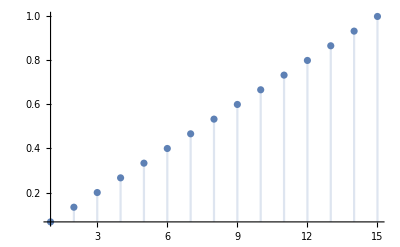

```mathematica
DiscretePlot[wy,{y,1,f},PlotRange->Full]
```

```mathematica
wy
```

```mathematica
Clear[a]
```

```mathematica
Integrate[q*Exp[-q*x],{q,0,1}]
```

```mathematica
Integrate[(1-Exp[-x]* (1+x))/x^2,{x,0,a}]
```

ConditionalExpression[(-1+a+ⅇ^-a)/a, Re[a]>0]

```mathematica
cdfexpunif
```

```mathematica
cdfexpunif = 1-0.09516258196404048/x
```

1-0.0951626/x

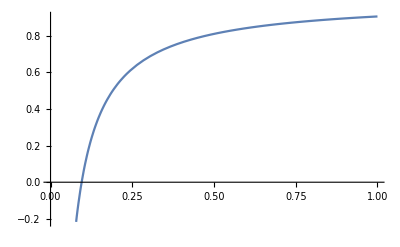

```mathematica
Plot[cdfexpunif,{x,0,1}]
```

```mathematica
h[x_]:=Piecewise[{{1-(Exp[-a*x]-Exp[-b*x])/ (x*(b-a)),x>=0},{0,x<0}}]
```

```mathematica
a=0.05
b=0.1
```

0.05

0.1

```mathematica
pk2 = NIntegrate[1/f*h[Floor[(k+x)/f]*f-x],{x,0,f}]
```

NIntegrate::inumr: The integrand 1/15 (Piecewise[{{1-(20. (Times[«2»]+Power[«2»]))/Plus[«2»], -x+15 Floor[«1»]≥0}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,15}}.

NIntegrate[h[Floor[(k+x)/f] f-x]/f,{x,0,f}]

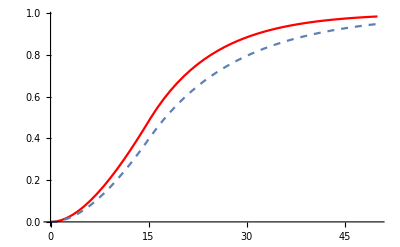

```mathematica
Show[Plot[pk,{k,0,50}, PlotStyle->Red], Plot[pk2,{k,0,50},  PlotStyle->Dashed]]
```

```mathematica
deltaf = 1/f*Integrate[h[x],{x,0,f},Assumptions->f∈Reals]
```

Piecewise[{{(a f-b f-Gamma[0,a f]+Gamma[0,b f]-Log[a]+Log[b])/(a-b), f>0}, {0, True}}]/f

```mathematica
Simplify[deltaf]
```

Integrate[Piecewise[{{1+(ⅇ^(a (-f+x))-ⅇ^(b (-f+x)))/((a-b) (f-x)), f≥x}, {0, True}}],{x,0,f},Assumptions→f∈ℝ]/f

```mathematica
h[x]
```

h[x]

```mathematica
lamT = 20
s=15
```

20

15

```mathematica
pois[k_] :=Exp[-lamT]*(lamT^k)/k!
```

```mathematica
Simplify[CDF[PoissonDistribution[lamT],10]]
```

991393769/(189 ⅇ^20)

```mathematica
D0[x_]:=1-Sum[pois[k],{k,0,x}]
```

```mathematica
g[x_]:=Piecewise[{{1-Exp[-θ*x] ,x>=0},{0,x<0}}]
```

```mathematica
θ=0.1
```

0.1

```mathematica
κ=10
```

10

```mathematica
T=15
```

15

```mathematica
bbar = N[lamT-Sum[D0[j],{j,0,s-1}]]
```

5.25041

```mathematica
p=1-bbar/(bbar+lamT)
```

0.792066

```mathematica
deltait = Integrate[1/T*g[(Floor[(t+x)/T]-i)*T-x],{x,0,T}]
```

∫_0^15 1/15 (Piecewise[{{1-ⅇ^(-0.1 (-x+15 (-i+Floor[(t+x)/15]))), -x+15 (-i+Floor[(t+x)/15])≥0}, {0, True}}])ⅆx

```mathematica
pik = p*((1-p)^i)/(1-(1-p)^(κ+1))
```

0.896602 0.103398^i

```mathematica
deltat = Sum[((1-p)^i)*p*deltait,{i,0,Infinity}]
```

∑_(i=0)^∞ 0.792066 0.207934^i ∫_0^15 1/15 (Piecewise[{{1-ⅇ^(-0.1 (-x+15 (-i+Floor[(t+x)/15]))), -x+15 (-i+Floor[(t+x)/15])≥0}, {0, True}}])ⅆx

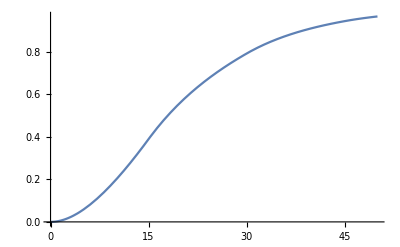

```mathematica
Plot[deltat,{t,0,50}]
```

```mathematica
ds = Import["C:\\Users\\Rohan Bapat\\Documents\\Projects\\Immunization Supply Chain\\immunization_supply_chain\\inputs\\total_delay_cdf_perfect_backlogging_s15_kappa10.csv","Dataset"]
```

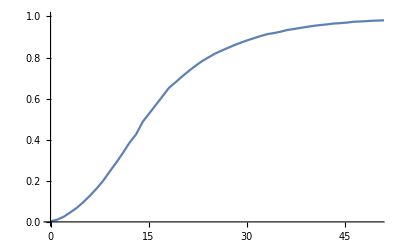

```mathematica
ListLinePlot[ds[All,2],DataRange->{0,150}, PlotRange->{{0,50},{0,1}}]
```

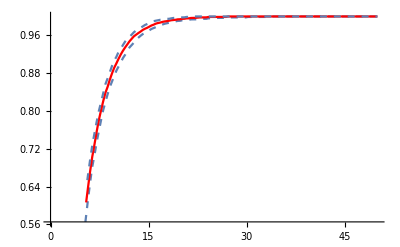

```mathematica
Show[ListLinePlot[ds[All,2], DataRange->{0,50},PlotStyle->Dashed],ListLinePlot[ds[All,3], DataRange->{0,50},PlotStyle->Red],ListLinePlot[ds[All,4], DataRange->{0,50},PlotStyle->Dashed]]
```

```mathematica
Show[Plot[deltat,{t,0,50}, PlotStyle->Blue],ListLinePlot[ds[All,2],DataRange->{0,150}, PlotRange->{{0,50},{0,1}},PlotStyle->Dashed],ListLinePlot[ds[All,3],DataRange->{0,150}, PlotRange->{{0,50},{0,1}},PlotStyle->Red],ListLinePlot[ds[All,4], DataRange->{0,150}, PlotRange->{{0,50},{0,1}},PlotStyle->Dashed]]
```

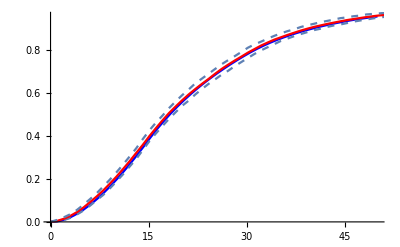

```mathematica
deltait/.t->10
```

0.245253